```mathematica
evShifted={-1.3373203533772653,-0.18643394310640815,-0.07105746371822974,-0.037407168791812495,-0.023050971814825516,-0.01561839001324472,-0.01127779477469204,-0.008524333162924336,-0.006668809821686494,-0.005359292793286841,-0.004400800990534748,-0.003678219961269491,-0.0031200305705318954,-0.0026798978946942498,-0.0023267324917313204,-0.0020390441242952306,-0.0018015927858030523,-0.001603327672349053,-0.0014360776077175785,-0.0012936953465683132}
```

{-1.33732,-0.186434,-0.0710575,-0.0374072,-0.023051,-0.0156184,-0.0112778,-0.00852433,-0.00666881,-0.00535929,-0.0044008,-0.00367822,-0.00312003,-0.0026799,-0.00232673,-0.00203904,-0.00180159,-0.00160333,-0.00143608,-0.0012937}

```mathematica
Vs2[r_]=- α/r Erf[r/(√2 a)]+c2 a^2 δa[r]+d1 a^4 Laplacian[δa[r],{r,θ,ϕ},"Spherical"];
```

```mathematica
δ50[-1/#-(1.0415223038416566 ⅇ^(-0.9990999998788636#))/#&]
```

NDSolve::precw: 参数函数的精度 ({{2. (1/10000000000+1/r+1.04152 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (50.).

NDSolve::precw: 参数函数的精度 ({{2. (1/100000+1/r+1.04152 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (50.).

NDSolve::precw: 参数函数的精度 ({{2. (0.001+1/r+1.04152 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (50.).

General::stop: 在本次计算中，NDSolve::precw 的进一步输出将被抑制.

FindRoot::precw: 参数函数的精度 (-0.0050548676284763871906775968288150267415083678453==0.0447214 Cot[2.23607+δ]) 小于 WorkingPrecision (30.).

FindRoot::precw: 参数函数的精度 (-0.0790497090489487333225391318363253476866298078556==0.0774597 Cot[3.87298+δ]) 小于 WorkingPrecision (30.).

FindRoot::precw: 参数函数的精度 (-0.352410573588944237735496186915957915248473388101==0.118322 Cot[5.91608+δ]) 小于 WorkingPrecision (30.).

General::stop: 在本次计算中，FindRoot::precw 的进一步输出将被抑制.

{-0.000211093311809286165789171204857,-0.0662106632226259687984386121924,-0.552719070259565125771447801683,-1.5066298005994241840443171397,0.043182197643211050684305606067,-0.8636644443359933236988993029,-0.167925984441675596289756756021,0.71872904284898136329483371992,-0.109908952376440067532850721497,0.598060586267498339383747118929,-1.00406980402453018267149794031,1.54766568306007940731233784}

```mathematica
a=1;δa[r_]=(E^(-r^2/(2 a^2)))/((2π)^(3/2)a^3);
```

```mathematica
- 1/# Erf[#/(√2 a)]+c2 a^2 δa[#]+d1 a^4 Laplacian[δa[#],{#,θ,ϕ},"Spherical"]&[r]
```

(c2 ⅇ^(-r^2/2))/(2 √2 π^(3/2))+d1 (-(3 ⅇ^(-r^2/2))/(2 √2 π^(3/2))+(ⅇ^(-r^2/2) r^2)/(2 √2 π^(3/2)))-Erf[r/(√2)]/r

```mathematica
δ50e[en_,V_]:=Module[{sol,δs,δr,r1=50,r2=u0},
k=√(2en);sol=Flatten@NDSolve[{u''[r]+α(en-V[r])u[r]==0,u'[r2]==1,u[r2]==u0},u,{r,r1,r2},AccuracyGoal->20,PrecisionGoal->10,WorkingPrecision->50, MaxSteps->Infinity,InterpolationOrder->All,Method->{"Shooting","StartingInitialConditions"->{u[r2]==u0,u'[r2]==1}}];
δs=FindRoot[u'[r1]/u[r1]==k Cot[k r1+δ]/.sol,{δ,0},WorkingPrecision->30,AccuracyGoal->Infinity,PrecisionGoal->20];
δr=δ/.δs;
δr=NestWhile[Sign[#](Abs[#]-π)&,δr,Abs[#]>π/2&]
]
```

```mathematica
k1=√(2 10^-10);
k2=√(2 10^-5);
FindRoot[{
δ/.First@FindRoot[u'[50]/u[50]==k1 Cot[k1 50+δ]/.Flatten@NDSolve[{u''[r]+α(10^-10-Vs2[r])u[r]==0,u'[u0]==1,u[u0]==u0},u,{r,50,u0},AccuracyGoal->20,PrecisionGoal->10,WorkingPrecision->50, MaxSteps->Infinity,InterpolationOrder->All,Method->{"Shooting","StartingInitialConditions"->{u[u0]==u0,u'[u0]==1}}],{δ,0},WorkingPrecision->30,AccuracyGoal->Infinity,PrecisionGoal->20]==%121[[1]],δ/.First@FindRoot[u'[50]/u[50]==k2 Cot[k2 50+δ]/.Flatten@NDSolve[{u''[r]+α(10^-5-Vs2[r])u[r]==0,u'[u0]==1,u[u0]==u0},u,{r,50,u0},AccuracyGoal->20,PrecisionGoal->10,WorkingPrecision->50, MaxSteps->Infinity,InterpolationOrder->All,Method->{"Shooting","StartingInitialConditions"->{u[u0]==u0,u'[u0]==1}}],{δ,0},WorkingPrecision->30,AccuracyGoal->Infinity,PrecisionGoal->20]==%121[[1]]
},{{c2,-43.,-50.},{d1,-7.,-8.}}]
```

NDSolve::precw: 参数函数的精度 ({{2. (1/10000000000-1/2 Power[«2»] c2 Power[«2»] Power[«2»]-d1 Plus[«2»]+2. Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (50.).

NDSolve::ndnum: 在 r == 1.0000000000000000209225608301284726753266340892878×10^-8 处碰到一个导数的非数值量.

ReplaceAll::reps: {NDSolve[{2. (1/10000000000+Times[«5»]+Times[«3»]+Times[«3»]) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},u,{r,50,1.×10^-8},AccuracyGoal→20,PrecisionGoal→10,WorkingPrecision→50,MaxSteps→∞,InterpolationOrder→All,Method→{Shooting,StartingInitialConditions→{u[«1»]==1.×10^-8,(«1»)^(«1»)[«1»]==1}}]} 既不是替换规则列表，也不是一个有效的分派表，因此无法用来替换.

NDSolve::precw: 参数函数的精度 ({{2. (1.×10^-10-0.0634936 Power[«2»] c2-1. d1 Plus[«2»]+2. Power[«2»] Erf[«1»]) u[r]+u''[r]==0.,u'[1.×10^-8]==1.,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (50.).

NDSolve::ndnum: 在 r == 1.0000000000000000209225608301284726753266340892878×10^-8 处碰到一个导数的非数值量.

ReplaceAll::reps: {NDSolve[{2. (1.×10^-10+Times[«3»]+Times[«3»]+Times[«3»]) u[r]+u''[r]==0.,u'[1.×10^-8]==1.,u[1.×10^-8]==1.×10^-8},u,{r,50.,1.×10^-8},AccuracyGoal→20.,PrecisionGoal→10.,WorkingPrecision→50.,MaxSteps→∞,InterpolationOrder→All,Method→{Shooting,StartingInitialConditions→{u[«1»]==1.×10^-8,(«1»)^(«1»)[«1»]==1.}}]} 既不是替换规则列表，也不是一个有效的分派表，因此无法用来替换.

General::stop: 在本次计算中，ReplaceAll::reps 的进一步输出将被抑制.

FindRoot::nlnum: 在 {δ} = {0.} 处，函数值 {u'[50.]/u[50.]==0.02/.NDSolve[{2. Plus[«4»] u[«1»]+u''[r]==0.,u'[1.×10^-8]==1.,u[1.×10^-8]==1.×10^-8},u,{r,50.,1.×10^-8},AccuracyGoal→20.,PrecisionGoal→10.,WorkingPrecision→50.,MaxSteps→∞,InterpolationOrder→All,Method→{Shooting,StartingInitialConditions→{Equal[«2»],Equal[«2»]}}]} 不是由数字组成的维度为 {1} 的列表.

NDSolve::precw: 参数函数的精度 ({{2. (1/10000000000-1/2 Power[«2»] c2 Power[«2»] Power[«2»]-d1 Plus[«2»]+2. Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (50.).

General::stop: 在本次计算中，NDSolve::precw 的进一步输出将被抑制.

NDSolve::ndnum: 在 r == 1.0000000000000000209225608301284726753266340892878×10^-8 处碰到一个导数的非数值量.

General::stop: 在本次计算中，NDSolve::ndnum 的进一步输出将被抑制.

FindRoot::nlnum: 在 {δ} = {0.} 处，函数值 {u'[50.]/u[50.]==0.0196656/.NDSolve[{2. Plus[«4»] u[«1»]+u''[r]==0.,u'[1.×10^-8]==1.,u[1.×10^-8]==1.×10^-8},u,{r,50.,1.×10^-8},AccuracyGoal→20.,PrecisionGoal→10.,WorkingPrecision→50.,MaxSteps→∞,InterpolationOrder→All,Method→{Shooting,StartingInitialConditions→{Equal[«2»],Equal[«2»]}}]} 不是由数字组成的维度为 {1} 的列表.

FindRoot::nlnum: 在 {c2,d1} = {-43.,-7.} 处，函数值 {δ/.{-0.115356==0.0000141421 Cot[Plus[«2»]]}==-0.000211093,δ/.{-0.115766==0.00447214 Cot[Plus[«2»]]}==-0.000211093} 不是由数字组成的维度为 {2} 的列表.

General::stop: 在本次计算中，FindRoot::nlnum 的进一步输出将被抑制.

FindRoot[{δ/.First[FindRoot[u'[50]/u[50]==k1 Cot[k1 50+δ]/.Flatten[NDSolve[{u''[r]+α (1/10^10-Vs2[r]) u[r]==0,u'[u0]==1,u[u0]==u0},u,{r,50,u0},AccuracyGoal→20,PrecisionGoal→10,WorkingPrecision→50,MaxSteps→∞,InterpolationOrder→All,Method→{Shooting,StartingInitialConditions→{u[u0]==u0,u'[u0]==1}}]],{δ,0},WorkingPrecision→30,AccuracyGoal→∞,PrecisionGoal→20]]==%121⟦1⟧,δ/.First[FindRoot[u'[50]/u[50]==k2 Cot[k2 50+δ]/.Flatten[NDSolve[{u''[r]+α (1/10^5-Vs2[r]) u[r]==0,u'[u0]==1,u[u0]==u0},u,{r,50,u0},AccuracyGoal→20,PrecisionGoal→10,WorkingPrecision→50,MaxSteps→∞,InterpolationOrder→All,Method→{Shooting,StartingInitialConditions→{u[u0]==u0,u'[u0]==1}}]],{δ,0},WorkingPrecision→30,AccuracyGoal→∞,PrecisionGoal→20]]==%121⟦1⟧},{{c2,-43.,-50.},{d1,-7.,-8.}}]

General::stop: 在本次计算中，FindRoot::nlnum 的进一步输出将被抑制.

FindRoot::nlnum: 在 {c2,d1} = {-43.,-7.} 处，函数值 {δ/.{δ→15.7071}==-0.000211093,δ/.{δ→2.87937}==-0.000211093} 不是由数字组成的维度为 {2} 的列表.

FindRoot::nlnum: 在 {δ} = {0.} 处，函数值 {u'[50.]/u[50.]==0.0196656/.NDSolve[{2. Plus[«4»] u[«1»]+u''[r]==0.,u'[1.×10^-8]==1.,u[1.×10^-8]==1.×10^-8},u,{r,50.,1.×10^-8},AccuracyGoal→20.,PrecisionGoal→10.,WorkingPrecision→50.,MaxSteps→∞,InterpolationOrder→All,Method→{Shooting,StartingInitialConditions→{Equal[«2»],Equal[«2»]}}]} 不是由数字组成的维度为 {1} 的列表.

General::stop: 在本次计算中，NDSolve::ndnum 的进一步输出将被抑制.

NDSolve::ndnum: 在 r == 1.0000000000000000209225608301284726753266340892878×10^-8 处碰到一个导数的非数值量.

General::stop: 在本次计算中，NDSolve::precw 的进一步输出将被抑制.

NDSolve::precw: 参数函数的精度 ({{2. (1/100000-1/2 Power[«2»] c2 Power[«2»] Power[«2»]-d1 Plus[«2»]+2. Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (50.).

FindRoot::nlnum: 在 {δ} = {0.} 处，函数值 {u'[50.]/u[50.]==0.02/.NDSolve[{2. Plus[«4»] u[«1»]+u''[r]==0.,u'[1.×10^-8]==1.,u[1.×10^-8]==1.×10^-8},u,{r,50.,1.×10^-8},AccuracyGoal→20.,PrecisionGoal→10.,WorkingPrecision→50.,MaxSteps→∞,InterpolationOrder→All,Method→{Shooting,StartingInitialConditions→{Equal[«2»],Equal[«2»]}}]} 不是由数字组成的维度为 {1} 的列表.

General::stop: 在本次计算中，ReplaceAll::reps 的进一步输出将被抑制.

ReplaceAll::reps: {NDSolve[{2. (1.×10^-10+Times[«3»]+Times[«3»]+Times[«3»]) u[r]+u''[r]==0.,u'[1.×10^-8]==1.,u[1.×10^-8]==1.×10^-8},u,{r,50.,1.×10^-8},AccuracyGoal→20.,PrecisionGoal→10.,WorkingPrecision→50.,MaxSteps→∞,InterpolationOrder→All,Method→{Shooting,StartingInitialConditions→{u[«1»]==1.×10^-8,(«1»)^(«1»)[«1»]==1.}}]} 既不是替换规则列表，也不是一个有效的分派表，因此无法用来替换.

NDSolve::ndnum: 在 r == 1.0000000000000000209225608301284726753266340892878×10^-8 处碰到一个导数的非数值量.

NDSolve::precw: 参数函数的精度 ({{2. (1.×10^-10-0.0634936 Power[«2»] c2-1. d1 Plus[«2»]+2. Power[«2»] Erf[«1»]) u[r]+u''[r]==0.,u'[1.×10^-8]==1.,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (50.).

ReplaceAll::reps: {NDSolve[{2. (1/10000000000+Times[«5»]+Times[«3»]+Times[«3»]) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},u,{r,50,1.×10^-8},AccuracyGoal→20,PrecisionGoal→10,WorkingPrecision→50,MaxSteps→∞,InterpolationOrder→All,Method→{Shooting,StartingInitialConditions→{u[«1»]==1.×10^-8,(«1»)^(«1»)[«1»]==1}}]} 既不是替换规则列表，也不是一个有效的分派表，因此无法用来替换.

NDSolve::ndnum: 在 r == 1.0000000000000000209225608301284726753266340892878×10^-8 处碰到一个导数的非数值量.

NDSolve::precw: 参数函数的精度 ({{2. (1/10000000000-1/2 Power[«2»] c2 Power[«2»] Power[«2»]-d1 Plus[«2»]+2. Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (50.).

NDSolve::precw: 参数函数的精度 ({{2. (1/10000000000-1/2 Power[«2»] c2 Power[«2»] Power[«2»]-d1 Plus[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (50.).

NDSolve::ndnum: 在 r == 1.0000000000000000209225608301284726753266340892878×10^-8 处碰到一个导数的非数值量.

ReplaceAll::reps: {NDSolve[{2. (1/10000000000+Times[«5»]+Times[«3»]+Times[«2»]) u[r]+u''[r]==0,u'[1.×10^-8]==1,u[1.×10^-8]==1.×10^-8},u,{r,50,1.×10^-8},AccuracyGoal→20,PrecisionGoal→10,WorkingPrecision→50,MaxSteps→∞,InterpolationOrder→All,Method→{Shooting,StartingInitialConditions→{u[«1»]==1.×10^-8,(«1»)^(«1»)[«1»]==1}}]} 既不是替换规则列表，也不是一个有效的分派表，因此无法用来替换.

NDSolve::precw: 参数函数的精度 ({{2. (1.×10^-10-0.0634936 Power[«2»] c2-1. d1 Plus[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0.,u'[1.×10^-8]==1.,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (50.).

NDSolve::ndnum: 在 r == 1.0000000000000000209225608301284726753266340892878×10^-8 处碰到一个导数的非数值量.

ReplaceAll::reps: {NDSolve[{2. (1.×10^-10+Times[«3»]+Times[«3»]+Times[«2»]) u[r]+u''[r]==0.,u'[1.×10^-8]==1.,u[1.×10^-8]==1.×10^-8},u,{r,50.,1.×10^-8},AccuracyGoal→20.,PrecisionGoal→10.,WorkingPrecision→50.,MaxSteps→∞,InterpolationOrder→All,Method→{Shooting,StartingInitialConditions→{u[«1»]==1.×10^-8,(«1»)^(«1»)[«1»]==1.}}]} 既不是替换规则列表，也不是一个有效的分派表，因此无法用来替换.

General::stop: 在本次计算中，ReplaceAll::reps 的进一步输出将被抑制.

FindRoot::nlnum: 在 {δ} = {0.} 处，函数值 {u'[50.]/u[50.]==0.02/.NDSolve[{2. Plus[«4»] u[«1»]+u''[r]==0.,u'[1.×10^-8]==1.,u[1.×10^-8]==1.×10^-8},u,{r,50.,1.×10^-8},AccuracyGoal→20.,PrecisionGoal→10.,WorkingPrecision→50.,MaxSteps→∞,InterpolationOrder→All,Method→{Shooting,StartingInitialConditions→{Equal[«2»],Equal[«2»]}}]} 不是由数字组成的维度为 {1} 的列表.

NDSolve::precw: 参数函数的精度 ({{2. (1.×10^-10-0.0634936 Power[«2»] c2-1. d1 Plus[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0.,u'[1.×10^-8]==1.,u[1.×10^-8]==1.×10^-8},{},{},{},{}}) 小于 WorkingPrecision (50.).

General::stop: 在本次计算中，NDSolve::precw 的进一步输出将被抑制.

NDSolve::ndnum: 在 r == 1.0000000000000000209225608301284726753266340892878×10^-8 处碰到一个导数的非数值量.

General::stop: 在本次计算中，NDSolve::ndnum 的进一步输出将被抑制.

FindRoot::nlnum: 在 {δ} = {0.} 处，函数值 {u'[50.]/u[50.]==0.02/.NDSolve[{2. Plus[«4»] u[«1»]+u''[r]==0.,u'[1.×10^-8]==1.,u[1.×10^-8]==1.×10^-8},u,{r,50.,1.×10^-8},AccuracyGoal→20.,PrecisionGoal→10.,WorkingPrecision→50.,MaxSteps→∞,InterpolationOrder→All,Method→{Shooting,StartingInitialConditions→{Equal[«2»],Equal[«2»]}}]} 不是由数字组成的维度为 {1} 的列表.

General::stop: 在本次计算中，FindRoot::nlnum 的进一步输出将被抑制.

$Aborted

```mathematica
s=FindRoot[{f[evShifted[[20]],c2,d1][10^-10]==0(*,f[evShifted[[15]],c2,d1][10^-10]==0*),f[evShifted[[15]],c2,d1][10^-10]==0}/.With[{r1=10^-10,r2=2000},ParametricNDSolve[{(Vs2[r]) f[r]-1/2 f''[r]==e f[r],f[r2]==0,f'[r2]==-r1},f,{r,r2,r1},{e,c2,d1}]],{{c2,-43.,-50.},{d1,-7.,-8.}},WorkingPrecision->20,AccuracyGoal->6,PrecisionGoal->6,MaxIterations->10000]
sol=With[{r1=10^-10,r2=2000},ParametricNDSolve[{(Vs2[r]/.s) f[r]-1/2 f''[r]==e f[r],f[r2]==0,f'[r2]==-r1},f,{r,r2,r1},e]];
FindRoot[f[e][10^-9]==0/.sol,{e,-0.0053,-0.0054}(*{e,-0.0014,-0.0015}*)];
((e/.%)-evShifted[[10]])/evShifted[[10]]
FindRoot[f[e][10^-9]==0/.sol,(*{e,-0.0053,-0.0054}*)(*{e,-0.0014,-0.0015}*){e,-0.0023,-0.0024}];
((e/.%)-evShifted[[15]])/evShifted[[15]]
FindRoot[f[e][10^-10]==0/.sol,{e,-0.0014,-0.0015}];
((e/.%)-evShifted[[19]])/evShifted[[19]]
FindRoot[f[e][10^-10]==0/.sol,{e,-0.0012,-0.0013}];
((e/.%)-evShifted[[20]])/evShifted[[20]]
```

FindRoot::cvmit: 无法在 10000 次迭代中收敛到要求的准确度或者精度.

{c2→-50.,d1→-3.957668613273096578}

FindRoot::brmp: 根已经被机器精度紧密包围，但是函数值超过了绝对容差 1.05367×10^-8.

0.0000389268

FindRoot::brmp: 根已经被机器精度紧密包围，但是函数值超过了绝对容差 1.05367×10^-8.

2.46109×10^-6

FindRoot::brmp: 根已经被机器精度紧密包围，但是函数值超过了绝对容差 1.05367×10^-8.

-3.43077×10^-6

FindRoot::brmp: 根已经被机器精度紧密包围，但是函数值超过了绝对容差 1.05367×10^-8.

-4.06957×10^-6

{-1.46354,-0.18635,-0.0711248,-0.0374228,-0.0230558,-0.0156202,-0.0112786,-0.00852471,-0.006669,-0.0053594,-0.00440086,-0.00367826,-0.00312005,-0.00267991,-0.00232674,-0.00203905,-0.0018016,-0.00160333,-0.00143608,-0.0012937}

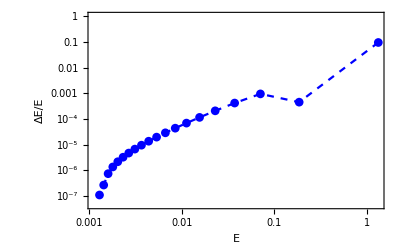

```mathematica
Module[{shift=10,d=2000,n=20,evc2},{evc2,efc2}=NDEigensystem[{shift f[r]+(Vs2[r]/.s) f[r]-1/2 f''[r](*+NeumannValue[0,r==d]*),DirichletCondition[f[r]==0,True]},f[r],{r,0,d},n,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.001}}},"Eigensystem"->{"Arnoldi",MaxIterations->Infinity}}];
evShiftedc2=evc2-shift]
δEVs2=Abs[(evShiftedc2-evShifted)/evShifted];
LδEVs2=Transpose@({-evShifted}~Join~{δEVs2});
ListLogLogPlot[LδEVs2,Frame->True,Joined->True,PlotMarkers->Automatic,ImageSize->Full,FrameLabel->{"E","ΔE/E"},RotateLabel->False,PlotStyle->{Dashed,Blue}]
```

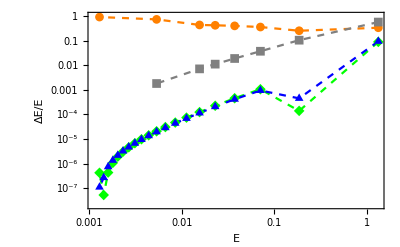

```mathematica
ListLogLogPlot[{LδE,Lδϵ,LδEVs1,LδEVs2},Frame->True,Joined->True,PlotMarkers->Automatic,ImageSize->Full,FrameLabel->{"E","ΔE/E"},RotateLabel->False,PlotStyle->{{Dashed,Orange},{Dashed,Gray},{Dashed,Green},{Dashed,Blue}}]
```